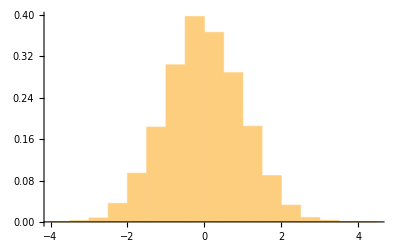

```mathematica
data1=RandomVariate[NormalDistribution[],10000];
Show[Histogram[data1,Automatic,"ProbabilityDensity"]]
```

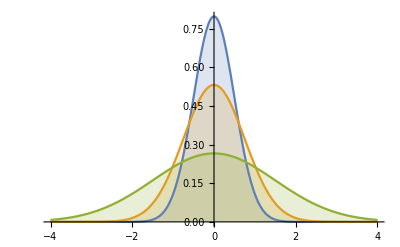

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{0.5,0.75,1.5}}]//Evaluate,{x,-4,4},Filling->Axis]
```

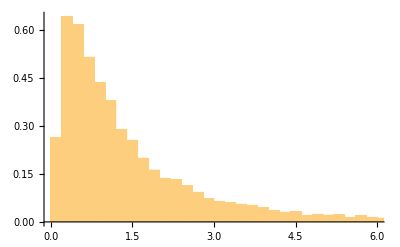

```mathematica
data2 = RandomVariate[LogNormalDistribution[0,1], 10000];
Show[Histogram[data2,Automatic,"ProbabilityDensity"]]
```

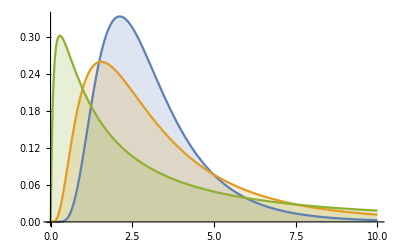

```mathematica
Plot[Table[PDF[LogNormalDistribution[1,σ],x],{σ,{0.5,0.75,1.5}}]//Evaluate,{x,0,10},Filling->Axis, PlotRange->All]
```

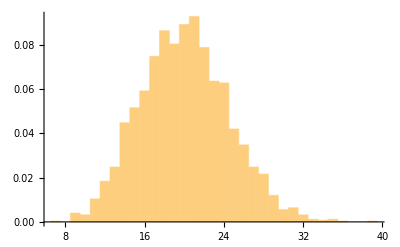

```mathematica
data3=RandomVariate[PoissonDistribution[20],2500];
Show[Histogram[data3,Automatic,"ProbabilityDensity"]]
```

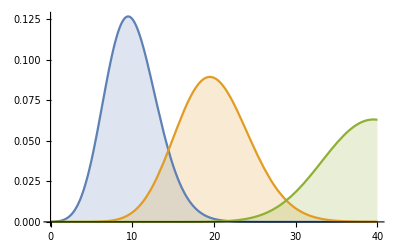

```mathematica
Plot[Table[PDF[PoissonDistribution[mu],x],{mu,{10,20,40}}]//Evaluate,{x,0,40},Filling->Axis]
```

```mathematica
h1=DistributionFitTest[data1,Automatic,"HypothesisTestData"];
h2=DistributionFitTest[data2,Automatic,"HypothesisTestData"];
```

```mathematica
h1["TestDataTable", All]
```

| Statistic | P-Value
Anderson-Darling | 0.344781 | 0.492261
Baringhaus-Henze | 0.450215 | 0.614334
Cramér-von Mises | 0.0586025 | 0.40213
Jarque-Bera ALM | 3.20757 | 0.196822
Kolmogorov-Smirnov | 0.0133364 | 0.362009
Kuiper | 0.0215099 | 0.465944
Mardia Combined | 3.20757 | 0.196822
Mardia Kurtosis | 0.491881 | 0.622804
Mardia Skewness | 2.93229 | 0.0868242
Pearson χ^2 | 44.3152 | 0.41598
Shapiro-Wilk | 0.999134 | 0.277976
Watson U^2 | 0.0493948 | 0.472199

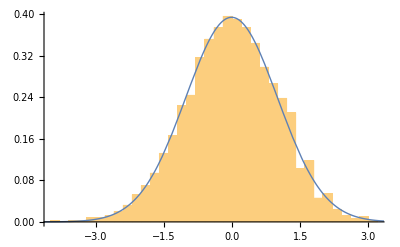

```mathematica
Show[Histogram[data1,Automatic,"ProbabilityDensity"],Plot[PDF[h1["FittedDistribution"],x],{x,-5,5},PlotStyle->Thick]]
```

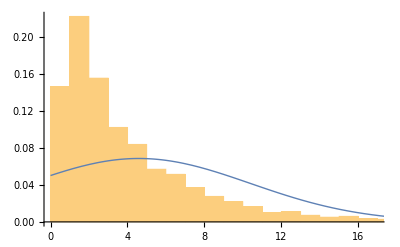

```mathematica
Show[Histogram[data2,Automatic,"ProbabilityDensity"],Plot[PDF[h2["FittedDistribution"],x],{x,0,20},PlotStyle->Thick]]
```